```mathematica
Clear["Global`*"]
```

## Constants

### Electron Charge (C)

```mathematica
e = 1.602 10^-19;
```

### Permitivitty of Free Space (F/m)

```mathematica
ϵ0 = 8.854 10^-12;
```

### Mass of Ytterbium (kg)

```mathematica
m = 2.84 10^-25;
```

### Bohr Magneton (J/T)

```mathematica
μB = 9.274 10^-24;
```

### Planck’s Reduced Constant (J.s)

```mathematica
ℏ = 1.055 10^-34;
```

## Initial Definitions

### Plot Settings

```mathematica
figoptions = {Frame -> True, FrameStyle -> 18,PlotStyle -> Thick,AspectRatio->0.5, ImageSize -> 500};
```

### Max motional state

```mathematica
nmax = 10;
```

### Motional states

```mathematica
nket[n_] := If[n≥0 && n ≤ nmax,SparseArray[{n+1,1}->1,{nmax+1,1}],0];
nbra[n_] := Conjugate[Transpose[nket[n]]];
```

### Motional State operators

```mathematica
a = Sum[√i nket[i-1].nbra[i],{i,1,nmax}];
adagger =  Sum[√i nket[i].nbra[i-1],{i,1,nmax}];
```

### Spin states

```mathematica
a_⊗b_ := KroneckerProduct[a,b];  (* shorthand for tensor product - use brackets if >2 subsystems e.g. (a ⊗ b) ⊗ c rather than a ⊗ b ⊗ c (order doesn't matter- tensor product is associative) *)
s0ket = {{1},{0}};
s1ket = {{0},{1}};
s0bra = ConjugateTranspose[s0ket];
s1bra = ConjugateTranspose[s1ket];
```

### Spin operators

```mathematica
sigmaplus = s1ket.s0bra;
sigmaminus = s0ket.s1bra;
```

### Spin Probability

```mathematica
iM[n_] := IdentityMatrix[n];
P[state_,ket_] := Abs[ConjugateTranspose[ket].(state.ConjugateTranspose[state]).ket]⟦1,1⟧   
Pspin[spinstate_,ket_] := P[spinstate⊗iM[nmax+1],ket]
P00[ket_] :=  Pspin[s0ket⊗s0ket,ket]
P01[ket_] :=  Pspin[s0ket⊗s1ket,ket]
P10[ket_] :=  Pspin[s1ket⊗s0ket,ket]
P11[ket_] :=  Pspin[s1ket⊗s1ket,ket]
```

## MS Hamiltonians

### Red Sideband

```mathematica
HRS1[t_,δ_,Ω_] := -(ℏ η Ω)/2(((sigmaplus⊗IdentityMatrix[2])⊗ a )Exp[-I δ t] + ((sigmaminus⊗IdentityMatrix[2]) ⊗ adagger)Exp[I δ t]);
HRS2[t_,δ_,Ω_] := (ℏ η Ω)/2(((IdentityMatrix[2]⊗sigmaplus)⊗ a)Exp[-I δ t] + ((IdentityMatrix[2]⊗sigmaminus) ⊗ adagger)Exp[I δ t]);
HRS1[t_,δ_,Ω_, ϕ_] := HRS1[t,δ,Ω] 
HRS2[t_,δ_,Ω_, ϕ_] := HRS2[t,δ,Ω]
```

### Blue Sideband

```mathematica
HBS1[t_,δ_,Ω_] := (ℏ η Ω)/2(((sigmaplus⊗IdentityMatrix[2])⊗ adagger )Exp[-I δ t] + ((sigmaminus⊗IdentityMatrix[2]) ⊗ a)Exp[I δ t]);
HBS2[t_,δ_,Ω_] := -(ℏ η Ω)/2(((IdentityMatrix[2]⊗sigmaplus)⊗ adagger)Exp[-I δ t] + ((IdentityMatrix[2]⊗sigmaminus) ⊗ a)Exp[I δ t]);
HBS1[t_,δ_,Ω_, ϕ_] := HBS1[t,δ,Ω] 
HBS2[t_,δ_,Ω_, ϕ_] := HBS2[t,δ,Ω] ;
```

## Simulation

### Input

```mathematica
dzB = 23.5;
ν = 2π √3 220.91 10^3;
η = 1/(√2)(μB dzB)/(ℏ ν)√(ℏ/(2m ν));
ΩD = 2π 80/2 10^3;
Ωr1 = ΩD;
Ωr2 = ΩD  ;
Ωb1 = ΩD ;
Ωb2 = ΩD ;

δMS = 2 η ΩD  ;
δA1 = 2 π 0;
δA2 =2 π 0;
δS = 2 π 0;

δr1 =- δMS + δA1 - δS;
δb1 = + δMS + δA1 + δS;
δr2 = - δMS + δA2 - δS;
δb2 =+ δMS + δA2 + δS;
tgate =  (2 π)/δMS
```

0.00233947

### Parameters

```mathematica
initialstate = (s0ket⊗s0ket)⊗nket[0];
tmin = 0;
tmax =2 tgate ;
```

### Solver

```mathematica
H[t_] :=HRS1[t,δr1,Ωr1, 0] + HRS2[t,δr2,Ωr2, 0] +HBS1[t,δb1,Ωb1, 0] + HBS2[t,δb2,Ωb2, 0] 
ProgressIndicator[Dynamic[currentTime],{0,tmax}];
currentTime=0;
timing =Timing[sol = NDSolve[I ℏ D[ψ[t],t] == Normal[H[t]].ψ[t] && ψ[0] ==Normal[initialstate] ,ψ,{t,tmin,tmax}, EvaluationMonitor:>(currentTime = t;)]];
ketevo[t_] := Evaluate[ψ[t]/.sol⟦1⟧];
```

### Output Plot

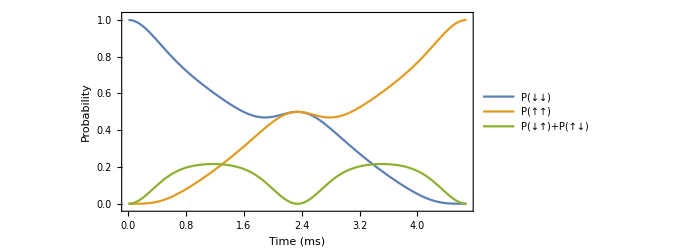

```mathematica
Plot[{Legended[P00[ketevo[t 10^-3]],"P(↓↓)"],Legended[P11[ketevo[t 10^-3]],"P(↑↑)"],Legended[P01[ketevo[t 10^-3]]+P10[ketevo[t 10^-3]],"P(↓↑)+P(↑↓)"]},{t,tmin 10^3,tmax 10^3},PlotRange -> {{tmin 10^3,tmax 10^3},{-0.02,1.02}},Evaluate[figoptions],FrameLabel->{"Time (ms)","Probability"}]
```

## Symmetric Detuning Scan

### Input

```mathematica
dzB = 23.5;
ν = 2π √3 220.91 10^3;
η = 1/(√2)(μB dzB)/(ℏ ν)√(ℏ/(2m ν));
ΩD = 2π 80/2 10^3;
Ωr1 = ΩD ;
Ωr2 = ΩD ;
Ωb1 = ΩD ;
Ωb2 = ΩD;

δMS = 2 η ΩD ;
δA1 = 2 π 0;
δA2 =-2 π 0;

tgate =(2 π)/δMS *1.0;

δr1 =- δMS + δA1;
δb1 = + δMS + δA1;
δr2 = - δMS + δA2;
δb2 =+ δMS + δA2;

δMSdet =  -  δMS;
δMSstep = δMS/10;
nSteps = 41;
δMSdet =  -  2 π 100;
δMSstep = 2 π 20;
nSteps = 11;
```

### Results

```mathematica
probsup = {50.532,53.191,54.255,56.383,55.851,65.957,62.766,71.277,76.064,80.319,82.979,76.064,63.298,62.766,68.085,31.383,78.192,66.489,67.553,68.617,68.617,67.021,72.873,66.489,72.34,32.447,54.787,61.17,62.766,71.277,78.723,80.851,72.34,68.085,71.808,65.957,61.17,63.298,57.979,60.106,50.532}/100;
probsdown = 1 - {50.532,53.191,54.255,56.383,55.851,65.957,62.766,71.277,76.064,80.319,82.979,76.064,63.298,62.766,68.085,31.383,78.192,66.489,67.553,68.617,68.617,67.021,72.873,66.489,72.34,32.447,54.787,61.17,62.766,71.277,78.723,80.851,72.34,68.085,71.808,65.957,61.17,63.298,57.979,60.106,50.532}/100;
```

### Simulation

```mathematica
GetKetEvo[δstep_] := Module[{sol, tmin, tmax, Teval,initialstate},
H[t_,δ_] :=HRS1[t,δr1 - δ,Ωr1] + HRS2[t,δr2 -δ,Ωr2] +HBS1[t,δb1 + δ,Ωb1] + HBS2[t,δb2 + δ,Ωb2] ;
initialstate = (s0ket⊗s0ket)⊗nket[0];
tmin = 0;
tmax = 2tgate;
Teval =tgate;
sol = NDSolve[I ℏ D[ψ[t],t] == Normal[H[t, δstep]].ψ[t] && ψ[0] ==Normal[initialstate] ,ψ,{t,tmin,tmax}];
ketevo[t_] := Evaluate[ψ[t]/.sol⟦1⟧];
{P00[ketevo[Teval]], P01[ketevo[Teval]]+P10[ketevo[Teval]], P11[ketevo[Teval]] }
];
ProbsList = Table[GetKetEvo[δMSdet + δMSstep i],{i, 0, nSteps}];
```

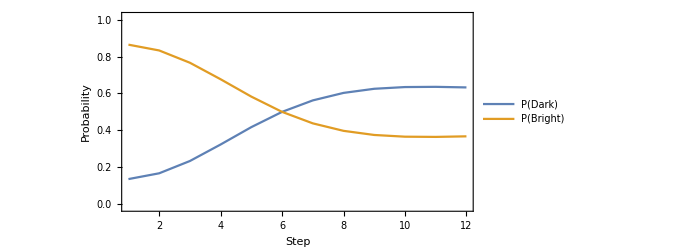

```mathematica
Show[ListLinePlot[{Legended[Transpose[ProbsList]⟦1⟧,"P(Dark)"],Legended[Transpose[ProbsList]⟦2⟧ + Transpose[ProbsList]⟦3⟧,"P(Bright)"]}, Evaluate[figoptions],FrameLabel->{"Step","Probability"}],PlotRange -> {All,{-0.02,1.02}}]
```

```mathematica
pbothion = {51.15154013596902,43.11628261930098,52.00566727813739,47.2839259274052,70.9079527332171,80.3820755389834,63.983015282964494,50.77703475683338,33.044225595613376,36.89651975202626}/100;
poneion = {25.503290815671537,36.545349636683675,29.140061508440297,29.473295465892203,23.49281926047227,14.19773850924766,20.284492227284524,22.44884614616528,24.316503148170867,24.66080491611058}/100;
pnoion = 1 - pbothion - poneion;
```

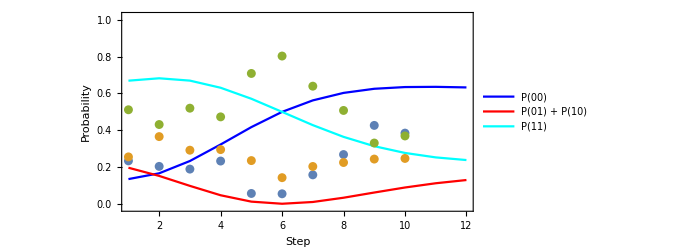

```mathematica
Show[ListLinePlot[{Legended[Transpose[ProbsList]⟦1⟧,"P(00)"],Legended[Transpose[ProbsList]⟦2⟧,"P(01) + P(10)"], Legended[Transpose[ProbsList]⟦3⟧,"P(11)"]}, PlotStyle->{{Blue}, {Red}, {Cyan}}, Evaluate[figoptions],FrameLabel->{"Step","Probability"}],
ListPlot[{pnoion, poneion, pbothion}],
PlotRange -> {All,{-0.02,1.02}}]
```

## Asymmetric 1 Detuning Scan

### Input

```mathematica
dzB = 23.5;
ν = 2π √3 220.91 10^3;
η = 1/(√2)(μB dzB)/(ℏ ν)√(ℏ/(2m ν));
ΩD = 2π 80/2 10^3;
Ωr1 = ΩD;
Ωr2 = ΩD  ;
Ωb1 = ΩD ;
Ωb2 = ΩD;

δMS = 2 η ΩD ;
 
δA12 = 2 π 40;
δmA12 = 2 π 80;
δA1 = δA12 + δmA12;
δA2 = δA12 - δmA12;
δS = 2 π 20;

tgate = (2 π)/δMS 1;

δr1 = -δMS + δA1 - δS;
δb1 =  δMS + δA1 + δS;
δr2 = - δMS + δA2 - δS;
δb2 =+ δMS + δA2 + δS;

δA1det = - 2π 400 ;
δA1step = 2 π 80;
nSteps = 10;
```

### Simulation

```mathematica
GetKetEvo[δstep_] := Module[{sol, tmin, tmax, initialstate, Teval},
H2[t_,δ_] :=HRS1[t,δr1 ,Ωr1] + HRS2[t,δr2+ δ ,Ωr2] +HBS1[t,δb1 ,Ωb1] + HBS2[t,δb2+ δ ,Ωb2] ;
H[t_,δ_] :=HRS1[t,δr1 + δ,Ωr1] + HRS2[t,δr2 ,Ωr2] +HBS1[t,δb1 + δ,Ωb1] + HBS2[t,δb2,Ωb2] ;
initialstate = (s0ket⊗s0ket)⊗nket[1];
tmin = 0;
tmax = 2tgate;
Teval =tgate;
sol = NDSolve[I ℏ D[ψ[t],t] == Normal[H[t, δstep]].ψ[t] && ψ[0] ==Normal[initialstate] ,ψ,{t,tmin,tmax}];
ketevo[t_] := Evaluate[ψ[t]/.sol⟦1⟧];
{P00[ketevo[Teval]], P01[ketevo[Teval]]+P10[ketevo[Teval]], P11[ketevo[Teval]] }
];
ProbsList = Table[GetKetEvo[δA1det + δA1step i],{i, 0, nSteps}];
```

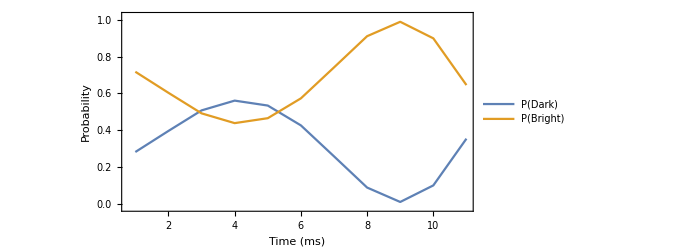

```mathematica
ListLinePlot[{Legended[Transpose[ProbsList]⟦1⟧,"P(Dark)"],Legended[Transpose[ProbsList]⟦2⟧ + Transpose[ProbsList]⟦3⟧,"P(Bright)"]}, Evaluate[figoptions],FrameLabel->{"Time (ms)","Probability"},PlotRange -> {All,{-0.02,1.02}}]
```

```mathematica
probszero = {23.94884247209434,20.9689133545087,30.3669115653044,33.71309766125438,51.988541611468364,44.36572084048964,42.486121198330494,33.86739315426745,18.22432382727633,13.291543671858683,5.49884200453225}/100;
probsone = {64.42460249428795,48.45579823760259,25.595907896500457,14.761714768416494,1.8172580288205342,6.4702801943811545,11.042258262601585,8.789388210577503,25.90294034219312,19.86671363068205,20.994317561944186}/100;
probstwo = 1 - probszero - probsone;
```

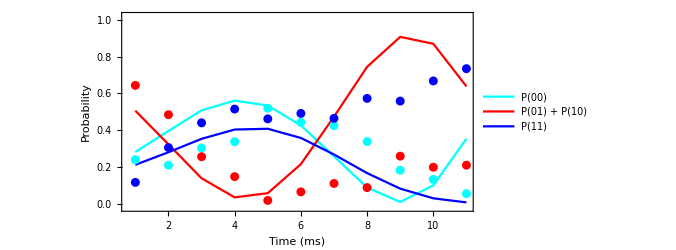

```mathematica
Show[ListLinePlot[{Legended[Transpose[ProbsList]⟦1⟧,"P(00)"],Legended[Transpose[ProbsList]⟦2⟧,"P(01) + P(10)"], Legended[Transpose[ProbsList]⟦3⟧,"P(11)"]}, PlotStyle->{{Cyan}, {Red}, {Blue}}, Evaluate[figoptions],FrameLabel->{"Time (ms)","Probability"},PlotRange -> {All,{-0.02,1.02}}],
ListPlot[{probszero, probsone, probstwo}, PlotStyle->{{Cyan}, {Red}, {Blue}}]]
```

## Asymmetric 1 and 2 Detuning Scan

### Input

```mathematica
dzB = 23.5;
ν = 2π √3 220.91 10^3;
η = 1/(√2)(μB dzB)/(ℏ ν)√(ℏ/(2m ν));
ΩD = 2π 80/2 10^3;
Ωr1 = ΩD ;
Ωr2 = ΩD ;
Ωb1 = ΩD ;
Ωb2 = ΩD  ;

δA12 = 2 π 40;
δmA12 = 2 π 80;
δA1 = δA12 + δmA12;
δA2 = δA12 - δmA12;
δS = 2 π 0;

tgate = (2 π)/δMS;

δr1 =- δMS + δA1 - δS;
δb1 = + δMS + δA1 + δS;
δr2 = - δMS + δA2 - δS;
δb2 =+ δMS + δA2 + δS;

δA1det = - 2π 400 ;
δA1step = 2 π 80;
nSteps = 10;
```

### Simulation

```mathematica
GetKetEvo[δstep_] := Module[{sol, tmin, tmax, Teval, initialstate},
H[t_,δ_] :=HRS1[t,δr1 + δ,Ωr1] + HRS2[t,δr2 + δ ,Ωr2] +HBS1[t,δb1 + δ,Ωb1] + HBS2[t,δb2 +δ,Ωb2] ;
initialstate = (s0ket⊗s0ket)⊗nket[0];
tmin = 0;
tmax = 2tgate;
Teval = tgate;
sol = NDSolve[I ℏ D[ψ[t],t] == Normal[H[t, δstep]].ψ[t] && ψ[0] ==Normal[initialstate] ,ψ,{t,tmin,tmax}];
ketevo[t_] := Evaluate[ψ[t]/.sol⟦1⟧];
{P00[ketevo[Teval]], P01[ketevo[Teval]]+P10[ketevo[Teval]], P11[ketevo[Teval]] }
];
ProbsList = Table[GetKetEvo[δA1det + δA1step i],{i, 0, nSteps}];
```

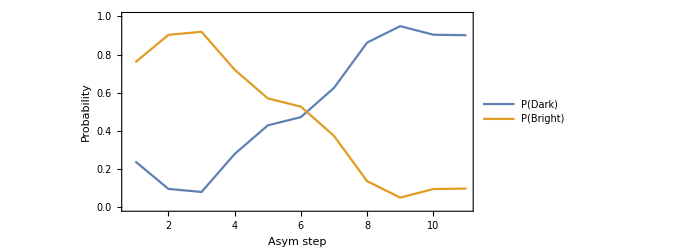

```mathematica
ListLinePlot[{Legended[Transpose[ProbsList]⟦1⟧,"P(Dark)"],Legended[Transpose[ProbsList]⟦2⟧ + Transpose[ProbsList]⟦3⟧,"P(Bright)"]}, Evaluate[figoptions],FrameLabel->{"Asym step","Probability"}, PlotRange->{All, {0, 1}}]
```

```mathematica
probszero = {48.75457041952787,37.21825487121781,12.883206104490782,19.818710588411314,45.51592360658702,41.25487433489292,22.072359910602128,11.145433632676982,6.058357984246278,4.583978828788121,2.955304180316901}/100;
probsone = {31.035213660294325,50.80451852013479,71.02580007668018,47.52223257785689,7.40384585412686,10.720419683741,20.896129520935876,12.02725575335164,11.963355599679566,13.47669826347436,20.962367485108146}/100;
probstwo = 1 - probszero - probsone;
```

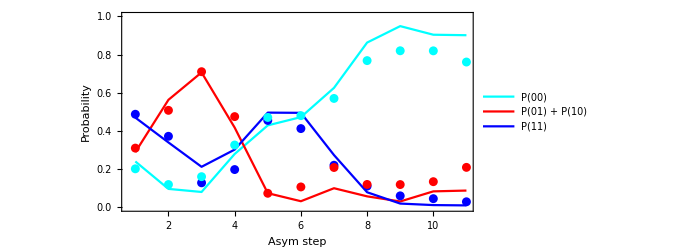

```mathematica
Show[ListLinePlot[{Legended[Transpose[ProbsList]⟦1⟧,"P(00)"],Legended[Transpose[ProbsList]⟦2⟧,"P(01) + P(10)"], Legended[Transpose[ProbsList]⟦3⟧,"P(11)"]}, PlotStyle->{{Cyan}, {Red}, {Blue}},Evaluate[figoptions],FrameLabel->{"Asym step","Probability"}, PlotRange->{All, {0, 1}}],
ListPlot[{probszero, probsone, probstwo}, PlotStyle->{{Blue}, {Red}, {Cyan}}]]
```

```mathematica
δA1/(2 π)
δA2/(2 π)
```

120

-40

## Asymmetric - 1 and 2 Detuning Scan

### Input

```mathematica
dzB = 23.5;
ν = 2π √3 220.91 10^3;
η = 1/(√2)(μB dzB)/(ℏ ν)√(ℏ/(2m ν));
ΩD = 2π 80/2 10^3;
Ωr1 = ΩD;
Ωr2 = ΩD;
Ωb1 = ΩD;
Ωb2 = ΩD ;

δMS = 2 η ΩD 1;

δA12 = 2 π 40;
δmA12 =2 π 80;
δA1 = δA12 + δmA12;
δA2 = δA12 - δmA12;
δS =2 π 40;

tgate = (2 π)/δMS;

δr1 =- δMS + δA1 - δS;
δb1 = + δMS + δA1 + δS;
δr2 = - δMS + δA2 - δS;
δb2 =+ δMS + δA2 + δS;

δA1det =- 2π 400 ;
δA1step = 2 π 80;
nSteps = 10;
```

### Simulation

```mathematica
GetKetEvo[δstep_] := Module[{sol, tmin, tmax, Teval,  initialstate},
H[t_,δ_] :=HRS1[t,δr1 + δ,Ωr1] + HRS2[t,δr2  - δ ,Ωr2] +HBS1[t,δb1 + δ,Ωb1] + HBS2[t,δb2- δ ,Ωb2] ;
initialstate = (s0ket⊗s0ket)⊗nket[0];
tmin = 0;
tmax = 2tgate;
Teval =2 tgate;
sol = NDSolve[I ℏ D[ψ[t],t] == Normal[H[t, δstep]].ψ[t] && ψ[0] ==Normal[initialstate] ,ψ,{t,tmin,tmax}];
ketevo[t_] := Evaluate[ψ[t]/.sol⟦1⟧];
{P00[ketevo[Teval]], P01[ketevo[Teval]]+P10[ketevo[Teval]], P11[ketevo[Teval]] }
];
ProbsList = Table[GetKetEvo[δA1det + δA1step i],{i, 0, nSteps}];
```

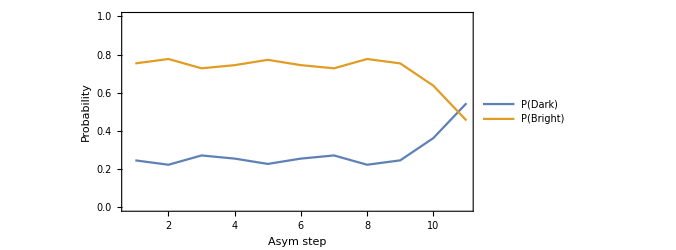

```mathematica
ListLinePlot[{Legended[Transpose[ProbsList]⟦1⟧,"P(Dark)"],Legended[Transpose[ProbsList]⟦2⟧ + Transpose[ProbsList]⟦3⟧,"P(Bright)"]}, Evaluate[figoptions],FrameLabel->{"Asym step","Probability"}, PlotRange->{All, {0, 1}}]
```

```mathematica
probszero = {58.3536203333406,60.87378005255398,56.02204399447652,39.610614283087045,33.381128570226274,47.654240944101396,43.887248958115784,45.78243400360958,63.25522968208894,46.72067528435568,49.0787468088886}/100;
probsone = {30.696231137765622,16.48156402639545,9.83361023399925,8.708344113237306,12.45975069588826,10.494431335388532,14.88951507576065,19.815281799677702,17.736968265001735,41.579518286353746,28.5883053367538146}/100;
probstwo = 1 - probszero - probsone;
```

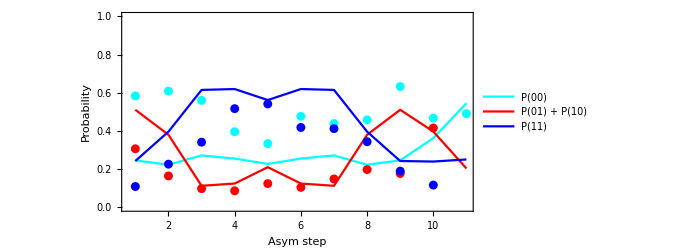

```mathematica
Show[ListLinePlot[{Legended[Transpose[ProbsList]⟦1⟧,"P(00)"],Legended[Transpose[ProbsList]⟦2⟧,"P(01) + P(10)"], Legended[Transpose[ProbsList]⟦3⟧,"P(11)"]}, PlotStyle->{{Cyan}, {Red}, {Blue}},Evaluate[figoptions],FrameLabel->{"Asym step","Probability"}, PlotRange->{All, {0, 1}}],
ListPlot[{probszero, probsone, probstwo}, PlotStyle->{{Cyan}, {Red}, {Blue}}]]
```

```mathematica
Transpose[ProbsList]⟦2⟧
```

{0.510856,0.380253,0.113144,0.125031,0.210529,0.125031,0.113144,0.380253,0.510856,0.397082,0.20383}

## Power 1 and 2 Detuning Scan

### Input

```mathematica
dzB = 23.5;
ν = 2π √3 220.91 10^3;
η = 1/(√2)(μB dzB)/(ℏ ν)√(ℏ/(2m ν));
ΩD = 2π 80/2 10^3;
Ωr1 = ΩD;
Ωr2 = ΩD;
Ωb1 = ΩD;
Ωb2 = ΩD ;

δMS = 2 η ΩD   ;
δA1 = 2 π 0;
δA2 = 2 π 0;
δS = -2 π 30;

tgate = (2 π)/δMS;

δr1 =- δMS + δA1 - δS;
δb1 = + δMS + δA1 + δS;
δr2 = - δMS + δA2 - δS;
δb2 =+ δMS + δA2 + δS;

δΩdet = - 2π 5000 ;
δΩstep = 2 π 500;
nSteps = 20;
```

### Simulation

```mathematica
GetKetEvo[δstep_] := Module[{sol, tmin, tmax,teval, initialstate},
H[t_,δ_] :=HRS1[t,δr1 ,Ωr1 + δ] + HRS2[t,δr2 ,Ωr2 + δ] +HBS1[t,δb1,Ωb1 + δ] + HBS2[t,δb2 ,Ωb2 + δ] ;
initialstate = (s0ket⊗s0ket)⊗nket[0];
tmin = 0;
tmax = 2 tgate;
teval =  tgate;
sol = NDSolve[I ℏ D[ψ[t],t] == Normal[H[t, δstep]].ψ[t] && ψ[0] ==Normal[initialstate] ,ψ,{t,tmin,tmax}];
ketevo[t_] := Evaluate[ψ[t]/.sol⟦1⟧];
{P00[ketevo[ teval]], P01[ketevo[teval]]+P10[ketevo[teval]], P11[ketevo[ teval]] }
];
ProbsList = Table[GetKetEvo[δΩdet + δΩstep i],{i, 0, nSteps}];
```

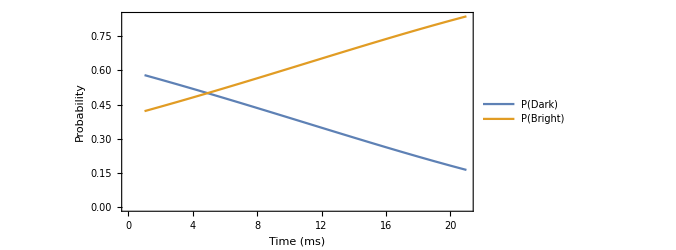

```mathematica
ListLinePlot[{Legended[Transpose[ProbsList]⟦1⟧,"P(Dark)"],Legended[Transpose[ProbsList]⟦2⟧ + Transpose[ProbsList]⟦3⟧,"P(Bright)"]}, Evaluate[figoptions],FrameLabel->{"Time (ms)","Probability"}]
```

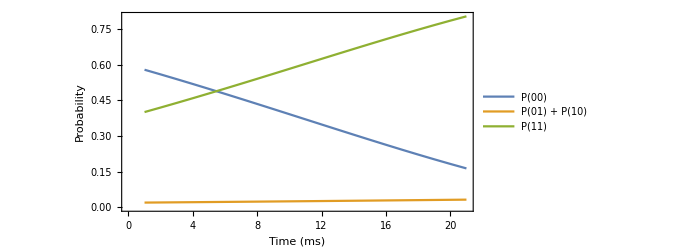

```mathematica
ListLinePlot[{Legended[Transpose[ProbsList]⟦1⟧,"P(00)"],Legended[Transpose[ProbsList]⟦2⟧,"P(01) + P(10)"], Legended[Transpose[ProbsList]⟦3⟧,"P(11)"]}, Evaluate[figoptions],FrameLabel->{"Time (ms)","Probability"}]
```

## Detuning Solver

### Stark Shift Equations

```mathematica
Subscript[Δϵ, Dplus1][ΩD_, ν_, δ0_, δa_] := -ΩD^2/2 (1/(- ν - δ0 - 2 δa) + 1/(ν + δ0 - 2 δa));
Subscript[Δϵ, Dminus1][ΩD_, ν_, δ0_, Δω_, δa_] := -ΩD^2/2 (1/(- ν - δ0 - Δω - 2 δa) + 1/(ν + δ0 - Δω- 2 δa));
aa1[Ωrf_, ν_, q_, Δω1_, x_] := Ωrf^2/4(1/(Δω1+ν+q+2x)+1/(Δω1-ν-q+2x));
Subscript[Δϵ, uplus1][Ωu_, ν_, δ0_, Ωμw_, δa_] := -Ωu^2/4 (1/(- ν - δ0 - Ωμw/(√2) + δa) + 1/(ν + δ0 - Ωμw/(√2)+ δa));
Subscript[Δϵ, uminus1][Ωu_, ν_, δ0_, Ωμw_, Δω_, δa_] := -Ωu^2/4 (1/(- ν - δ0 - Δω- Ωμw/(√2) - δa) + 1/(ν + δ0  - Δω- Ωμw/(√2)- δa));
Subscript[Δϵ, dplus1][Ωd_, ν_, δ0_, Ωμw_, δa_] := -Ωd^2/4 (1/(- ν - δ0 + Ωμw/(√2) + δa) + 1/(ν + δ0 + Ωμw/(√2)+ δa));
Subscript[Δϵ, dminus1][Ωd_, ν_, δ0_, Ωμw_, Δω_, δa_] := -Ωd^2/4 (1/(- ν - δ0 - Δω+Ωμw/(√2) - δa) + 1/(ν + δ0  - Δω+ Ωμw/(√2)- δa));
Subscript[Δϵ, stark][Ωrf_, ν_, δ0_, Ωμw_, Δω_, δa_] := Subscript[Δϵ, Dplus1][Ωrf/(√2), ν, δ0, δa] + Subscript[Δϵ, Dminus1][Ωrf/(√2), ν, δ0, Δω, δa] + Subscript[Δϵ, uplus1][Ωrf/2, ν, δ0,Ωμw,δa] + Subscript[Δϵ, uminus1][Ωrf/2, ν, δ0,Ωμw, Δω, δa] + Subscript[Δϵ, dplus1][Ωrf/2, ν, δ0,Ωμw,δa] + Subscript[Δϵ, dminus1][Ωrf/2, ν, δ0,Ωμw, Δω, δa];
```

### Solve Equation

```mathematica
dzB = 23.6;
Ωrf = 2 π 80/(√2) 10^3;
ΩD = Ωrf/(√2);
Ωμw = 2 π 22 10^3;
ν = 2 π 382.636 10^3;
η = 1/(√2)(μB dzB)/(ℏ ν)√(ℏ/(2m ν));
δ0 = 2 η ΩD ;
Δω1 = -2 π 14.718 10^3;
Δω2 = -2 π 27.492 10^3;
```

```mathematica
ΩD/(2π)
```

45000

```mathematica
Δϵ1[δa_] := Subscript[Δϵ, stark][Ωrf, ν, δ0, Ωμw, Δω1, δa];
Δϵ2[δa_] := Subscript[Δϵ, stark][Ωrf, ν, δ0, Ωμw, Δω2, δa];
sol1 = δa /.Solve[δa - Δϵ1[δa] == 0, δa];
sol2 = δa /.Solve[δa - Δϵ2[δa] == 0, δa];
stark1 = sol1 - Min[Abs[sol1]];
stark2 = sol2 - Min[Abs[sol2]];
If[Min[Abs[stark1]]==0,stark1 = Min[Abs[sol1]],stark1 = -Min[Abs[sol1]]];
If[Min[Abs[stark2]]==0,stark2 = Min[Abs[sol2]],stark2 = -Min[Abs[sol2]]];

Dataset[{{"Secular Frequency", "ν", ν/(2 π 10^3), "KHz"}, {"Frequency difference ion 1", "Δω", Δω1/(2 π 10^3), "KHz"}, {"Frequency difference ion 2", "Δω", Δω2/(2 π 10^3), "KHz"},
{"Stark shift ion 1", "δA1", stark1/(2 π), "Hz"},
{"Stark shift ion 2", "δA2", stark2/(2 π), "Hz"},
{"Gate detuning", "δS", δ0/(2 π), "Hz"},
{"Gate time", "T_gate", (2π)/δ0 1000, "ms"}}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

## Parity Detuning Scan

### Input

```mathematica
dzB = 23.5;
ν = 2π √3 220.91 10^3;
η = 1/(√2)(μB dzB)/(ℏ ν)√(ℏ/(2m ν));
ΩD = 2π 80/2 10^3;
Ωr1 = ΩD;
Ωr2 = ΩD  ;
Ωb1 = ΩD ;
Ωb2 = ΩD;

δMS = 2 η ΩD ;
 
δA1 = 2 π 0;
δA2 = 2 π 0;
δS = 2π 0;

tgate = (2 π)/δMS ;

δr1 =- δMS + δA1 - δS;
δb1 = + δMS + δA1 + δS;
δr2 = - δMS + δA2 - δS;
δb2 =+ δMS + δA2 + δS;

δϕdet = 0 ;
δϕstep = 2π/10;
nSteps = 11;
```

### Simulation

```mathematica
GetKetEvo[δstep_] := Module[{sol, tmin, tmax, initialstate, Teval},
H[t_,δ_] :=HRS1[t,δr1 + δ,Ωr1] + HRS2[t,δr2 ,Ωr2] +HBS1[t,δb1 + δ,Ωb1] + HBS2[t,δb2 ,Ωb2] ;
initialstate = (s0ket⊗s0ket)⊗nket[0];
tmin = 0;
tmax = 2tgate;
Teval =2 tgate;
sol = NDSolve[I ℏ D[ψ[t],t] == Normal[H[t, δstep]].ψ[t] && ψ[0] ==Normal[initialstate] ,ψ,{t,tmin,tmax}];
ketevo[t_] := Evaluate[ψ[t]/.sol⟦1⟧];
{P00[ketevo[Teval]], P01[ketevo[Teval]]+P10[ketevo[Teval]], P11[ketevo[Teval]] }
];
ProbsList = Table[GetKetEvo[δA1det + δA1step i],{i, 0, nSteps}];
```

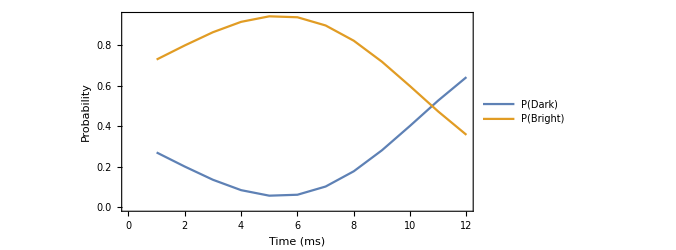

```mathematica
ListLinePlot[{Legended[Transpose[ProbsList]⟦1⟧,"P(Dark)"],Legended[Transpose[ProbsList]⟦2⟧ + Transpose[ProbsList]⟦3⟧,"P(Bright)"]}, Evaluate[figoptions],FrameLabel->{"Time (ms)","Probability"}]
```

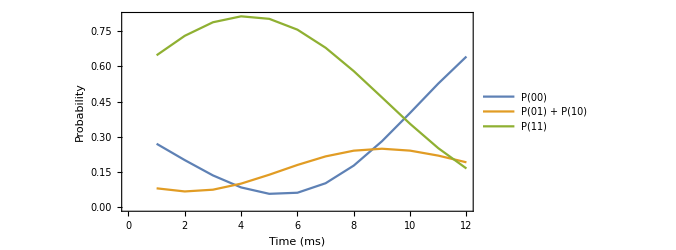

```mathematica
ListLinePlot[{Legended[Transpose[ProbsList]⟦1⟧,"P(00)"],Legended[Transpose[ProbsList]⟦2⟧,"P(01) + P(10)"], Legended[Transpose[ProbsList]⟦3⟧,"P(11)"]}, Evaluate[figoptions],FrameLabel->{"Time (ms)","Probability"}]
```